## The Anscombe’s quartet

The Anscombe’s quartet comprises four datasets, each containing eleven (x, y) points, that share nearly identical simple descriptive statistics—such as means and variances—yet exhibit markedly different distributions when graphed.

```mathematica
(*  Locate the Document and Files  *)
SetDirectory[NotebookDirectory[]];
FileNames[{"*.dat","*.xls*"}]
```

{Anscombe_quartet.xlsx,bloodtype.dat,enzyme.dat,geyser.dat}

```mathematica
anscombe=Import["Anscombe_quartet.xlsx"]
```

{{{x,y,x,y,x,y,x,y},{10.,8.04,10.,9.14,10.,7.46,8.,6.58},{8.,6.95,8.,8.14,8.,6.77,8.,5.76},{13.,7.58,13.,8.74,13.,12.74,8.,7.71},{9.,8.81,9.,8.77,9.,7.11,8.,8.84},{11.,8.33,11.,9.26,11.,7.81,8.,8.47},{14.,9.96,14.,8.1,14.,8.84,8.,7.04},{6.,7.24,6.,6.13,6.,6.08,8.,5.25},{4.,4.26,4.,3.1,4.,5.39,19.,12.5},{12.,10.84,12.,9.13,12.,8.15,8.,5.56},{7.,4.82,7.,7.26,7.,6.42,8.,7.91},{5.,5.68,5.,4.74,5.,5.73,8.,6.89}}}

```mathematica
Dimensions[anscombe]
```

{1,12,8}

```mathematica
anscombe=Flatten[anscombe,1]
```

{{x,y,x,y,x,y,x,y},{10.,8.04,10.,9.14,10.,7.46,8.,6.58},{8.,6.95,8.,8.14,8.,6.77,8.,5.76},{13.,7.58,13.,8.74,13.,12.74,8.,7.71},{9.,8.81,9.,8.77,9.,7.11,8.,8.84},{11.,8.33,11.,9.26,11.,7.81,8.,8.47},{14.,9.96,14.,8.1,14.,8.84,8.,7.04},{6.,7.24,6.,6.13,6.,6.08,8.,5.25},{4.,4.26,4.,3.1,4.,5.39,19.,12.5},{12.,10.84,12.,9.13,12.,8.15,8.,5.56},{7.,4.82,7.,7.26,7.,6.42,8.,7.91},{5.,5.68,5.,4.74,5.,5.73,8.,6.89}}

```mathematica
Dimensions[anscombe]
```

{12,8}

```mathematica
TableView[anscombe]
```

xyxyxyxy10.8.0410.9.1410.7.468.6.588.6.958.8.148.6.778.5.7613.7.5813.8.7413.12.748.7.719.8.819.8.779.7.118.8.8411.8.3311.9.2611.7.818.8.4714.9.9614.8.114.8.848.7.046.7.246.6.136.6.088.5.254.4.264.3.14.5.3919.12.512.10.8412.9.1312.8.158.5.567.4.827.7.267.6.428.7.915.5.685.4.745.5.738.6.89

The table contains 4 sets (quartet), each with x and y.
We get a first impression from simple descriptive statistics, i.e. mean, media, mode and standard deviation.

```mathematica
Mean[anscombe[[2;;,#]]]&/@ {1,3,5,7}
```

{9.,9.,9.,9.}

```mathematica
Mean[anscombe[[2;;,#]]]&/@ {2,4,6,8}
```

{7.50091,7.50091,7.5,7.50091}

```mathematica
Median[anscombe[[2;;,#]]]&/@ {1,3,5,7}
```

{9.,9.,9.,8.}

```mathematica
Median[anscombe[[2;;,#]]]&/@ {2,4,6,8}
```

{7.58,8.14,7.11,7.04}

```mathematica
Max[anscombe[[2;;,#]]]&/@ {1,3,5,7}
```

{14.,14.,14.,19.}

```mathematica
Max[anscombe[[2;;,#]]]&/@ {2,4,6,8}
```

{10.84,9.26,12.74,12.5}

```mathematica
StandardDeviation[anscombe[[2;;,#]]]&/@ {1,3,5,7}
```

{3.31662,3.31662,3.31662,3.31662}

```mathematica
StandardDeviation[anscombe[[2;;,#]]]&/@ {2,4,6,8}
```

{2.03157,2.03166,2.03042,2.03058}

The four datasets look very similar, only the medians hints to some differences.
Let’s do a linear fit with LinearModelFitpaclet:ref/LinearModelFit.

```mathematica
set1=anscombe[[2;;,1;;2]]
```

{{10.,8.04},{8.,6.95},{13.,7.58},{9.,8.81},{11.,8.33},{14.,9.96},{6.,7.24},{4.,4.26},{12.,10.84},{7.,4.82},{5.,5.68}}

```mathematica
set2=anscombe[[2;;,3;;4]];
```

```mathematica
set3=anscombe[[2;;,5;;6]];
```

```mathematica
set4=anscombe[[2;;,7;;8]];
```

```mathematica
lms1=LinearModelFit[set1,x,x]
```

FittedModel[3.00009+0.500091 x]

```mathematica
lms2=LinearModelFit[set2,x,x]
```

FittedModel[3.00091+0.5 x]

```mathematica
lms3=LinearModelFit[set3,x,x]
```

FittedModel[3.00245+0.499727 x]

```mathematica
lms4=LinearModelFit[set4,x,x]
```

FittedModel[3.00173+0.499909 x]

```mathematica
{lms1["RSquared"],lms2["RSquared"],lms3["RSquared"],lms4["RSquared"]}
```

{0.666542,0.666242,0.666324,0.666707}

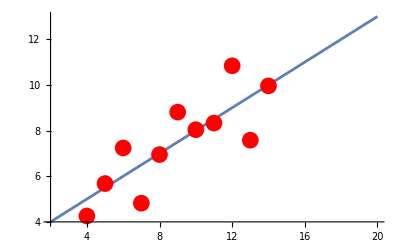

```mathematica
Show[{Plot[lms1[x],{x,2,20}],ListPlot[set1  ,PlotStyle->{Red,PointSize[0.03]}]}]
```

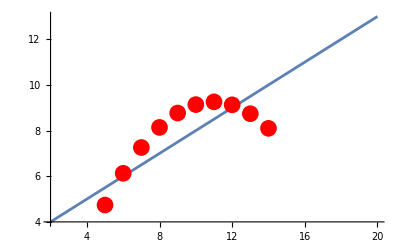

```mathematica
Show[{Plot[lms2[x],{x,2,20}],ListPlot[set2  ,PlotStyle->{Red,PointSize[0.03]}]}]
```

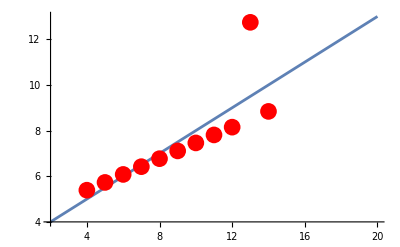

```mathematica
Show[{Plot[lms3[x],{x,2,20}],ListPlot[set3  ,PlotStyle->{Red,PointSize[0.03]}]}]
```

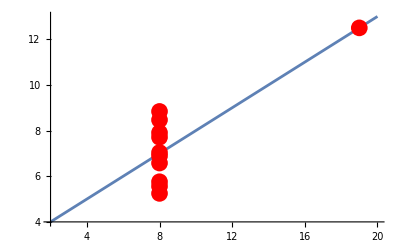

```mathematica
Show[{Plot[lms4[x],{x,2,20}],ListPlot[set4  ,PlotStyle->{Red,PointSize[0.03]}]}]
```

```mathematica
{
Show[{Plot[lms1[x],{x,2,20}],ListPlot[set1  ,PlotStyle->{Red,PointSize[0.03]}]}],Show[{Plot[lms2[x],{x,2,20}],ListPlot[set2  ,PlotStyle->{Red,PointSize[0.03]}]}] ,
Show[{Plot[lms3[x],{x,2,20}],ListPlot[set3  ,PlotStyle->{Red,PointSize[0.03]}]}] ,
Show[{Plot[lms4[x],{x,2,20}],ListPlot[set4  ,PlotStyle->{Red,PointSize[0.03]}]}] 
}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Simple descriptive statistics give a good first and quick impression but they can lead to wrong conclusions!
Is there a better fit for some sets in the Anscombe’s quartet?

FittedModel[18.6769-57.3659/x-0.419973 x]

0.964621

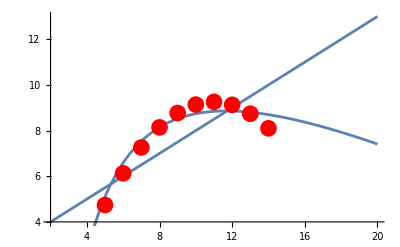

```mathematica
altlms2=LinearModelFit[set2,{x,1/x},x]
altlms2["RSquared"]
Show[{Plot[lms2[x],{x,2,20}],Plot[altlms2[x],{x,2,20}],ListPlot[set2  ,PlotStyle->{Red,PointSize[0.03]}]}]
```

Alternatively, we can let Mathematica find a function for us:

```mathematica
sugg2=FindFormula[set2,x]
```

-5.99573+2.78084 x-0.126713 x^2

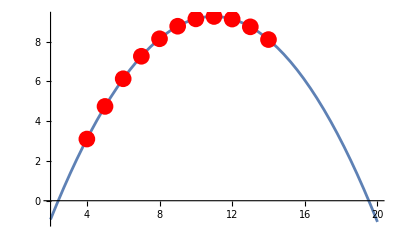

```mathematica
Show[{Plot[sugg2,{x,2,20}],ListPlot[set2  ,PlotStyle->{Red,PointSize[0.03]}]}]
```

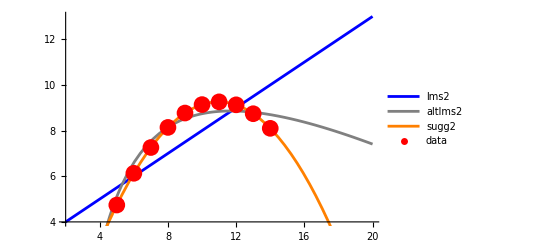

```mathematica
Show[Plot[lms2[x],{x,2,20},PlotStyle->Blue,PlotLegends->{"lms2"}],Plot[altlms2[x],{x,2,20},PlotStyle->Gray,PlotLegends->{"altlms2"}],Plot[sugg2,{x,2,20},PlotStyle->Orange,PlotLegends->{"sugg2"}],ListPlot[set2  ,PlotStyle->{Red,PointSize[0.03]},PlotLegends->{"data"}]]
```

```mathematica
|
```

```mathematica
altlms2=LinearModelFit[set2,{x,x^2},x]
```

FittedModel[-5.99573+2.78084 x-0.126713 x^2]

```mathematica
altlms2["RSquared"]
```

0.999999